# Simulating the Emergence of Reproductive and Parenting Strategies using Agent-Based Modeling with Evolutionary Game Theory

## Abstract

We’ll work on this during the last couple of sprints.

## Introduction

The processes by which life interacts with its environment, sustains itself, and continues on through its posterity (reproduces) are complex and intricately shaped by environmental factors and evolution. One interesting aspect of organism’s behavior is the reasons why organisms reproduce the way they do, and how they take care of their young: their reproductive and parenting behaviors. Agent-Based Modeling (ABM) simulations, while greatly simplified, can provide interesting theory that can provide a basis and a framework for actual studies of ecological behaviors and traits in organisms. Agent-Based Modeling simulations consist of agents that interact with each other and their environment through simple rules. As the simulation evolves through time, the rules produce interesting behavior among the agents that can be studied. These rules ideally mimic real life to create a realistic, albeit simplified, simulation.
	In this work, we apply Agent-Based Modeling and Evolutionary Game Theory in Wolfram Language to create a testing ground for investigating the emergence of reproductive and parenthood strategies in organisms. Specifically, through simulated genes dictating behavior through Evolutionary Game Theory, we explore two areas: 1) fecundity, and 2) parental feeding strategies. [describe fecundity and the feeding strategies in more detail]. With our model, we tweak environment setups, agent behavior, and other parameters of our model to analyze statistical data produced by the simulation and gain insights on reproductive and parenting strategies of organisms. In doing this, we perform experiments with [describe experiments]. Through these experiments, we explore two distinct, but interrelated questions: [questions]
	
[would like to put a bit about r/k selection in here as well, can be found in project plan.]

## High-Level Model Development

### [this is where we will include lit review and research to back up our model choices. I’m thinking that this will be similar to the implementation section of our project proposal and maybe include a little bit of our project plan as well.]

### Current Scope [<-- Replace this with a few sections giving a high-level description of how our model works, so that the following sections have a framing and don’t seem arbitrary.]

Currently, our model simulates the basic behaviors within a population, consisting of agents that move, search for and consume nearby food, and gain or lose energy. We’ve also created a visualization for our ABM so far.

## Model Parameters [what was the function for putting them in a little box again?]

[these have to be the first thing so that the rest of the comp notebook works, and everything has to be in order, so that’s why I rearranged the sections]

These are model parameters that set the rules for a simulation, and a user may freely tweak them to model certain environmental scenarios or use these as independent variables to run empirical experiments.

## Core Model

Before reproductive and parenting functions/strategies were implemented into agents, the core aspects of the model like agents that moved and consumed food were built first. For an agent to consume food to gain energy, a piece of food needs to be within the model’s proximity radius [is there a way to do inline code cells?]. Euclidian distance in the checkWithinRadius function is used to verify if a piece of food is close enough to an agent.

```mathematica
checkWithinRadius[p1_, p2_, r_] := EuclideanDistance[p1, p2] <= r;
```

## Reproduction

## Reproductive Strategies

## Parenting Strategies

## Model Propagation

### propogateModel[params_, model_]

This is the top-level timestep function that computes all of the helper functions at once to allow us to loop and update our simulation continuously.

## Visualization

To simulate how agents interact with one another in an environment, we created a square visualization window bounded by the parameter squareBounds to render agents, food/resources, energy levels, ages, and other characteristics for each timestep. The function first extracts all agent information from the main association. In particular, an important variable is span, which we use to scale the visualization with the size of the modeled world, so the display remains consistent even when the environment changes.

[btw the closing square bracket for this module below is in another cell].

```mathematica
displayGrid[model_, params_] := Module[
  {
    agents, foods, min, max, span, nAgents,
    hudPad, agentR, foodR, barW, barH, barGap,
    showEnergyBars, legendX, legendY, infoX, infoY,
    ageColor, ageTextColor, energyColor,
    chooseBarCenter, otherAgentPositions,
    agentGraphics, foodGraphics, legend, infoText
  },

  agents = model["agents"];
  foods = model["foods"];
  {min, max} = params["squareBounds"];
  span = max - min;
  nAgents = Length[agents];
```

Since the bounds of the environment can change, we scaled the graphics to the bound of the world. Specifically, if the environment is small, agents and food appear larger, whereas if the environment is large, the agents appear smaller. Additionally to keep the visualization clean and prevent the grid from looking ‘crowded’ as the population increases, we used the current population size to control how much detail to display. As a result, energy bars are only shown when there are less than 6 agents.

```mathematica
agentR = params["agentSize"]*span;
  foodR  = params["foodSize"]*span;

  barW = 0.10 span;
  barH = 0.015 span;
  barGap = 0.040 span;

  hudPad = 0.001 span;

  showEnergyBars = nAgents < 6;
```

The agents’ properties, such as age and energy level, are represented by color gradients. Specifically, age is shown by a green (young agent) to red (old agent) gradient. It is important to note that the agents’ ages are relative to their total lifespan. This allows us to display the age visually, without crowding the grid with other legends. We also switch the text color between black and white, depending on each agent’s age, to keep the age readable against different gradient colors. The energy of each agent is represented by a red-to-green bar, in which red represents low energy, while green represents a high energy. These energy levels are relative to the max energy defined in the associations.

```mathematica
ageColor[age_] := Blend[
    {Green, Yellow, Orange, Red},
    Clip[age/(0.3 params["lifespan"]), {0, 1}]
  ];

  ageTextColor[age_] := If[age < 0.6 params["lifespan"], Black, White];

  energyColor[frac_] := Blend[
    {Red, Yellow, Green},
    Clip[frac, {0, 1}]
  ];
```

Initially, we found it difficult to avoid overlap between text/agent information when agents are close together in the grid. So, to fix this, we wrote a helper rule to check agent positions and test multiple possible locations for the energy bar. Now, the function takes into account the positions above, below, left, and right, clips them to stay inside the grid, and, by using a scoring method, finds what position maximizes distance from nearby agents. Overall, this makes the visualization more readable.

```mathematica
otherAgentPositions[pos_] := DeleteCases[Lookup[agents, "pos"], pos];
  chooseBarCenter[pos_, others_] := Module[{candidates, scores}, candidates = {pos + {0, barGap}, pos + {0, -barGap}, pos + {barGap, 0}, pos + {-barGap, 0}};
    
    candidates = {
      {Clip[candidates[[1, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[1, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[2, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[2, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[3, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[3, 2]], {min + barH/2, max - barH/2}]},
      {Clip[candidates[[4, 1]], {min + barW/2, max - barW/2}],
       Clip[candidates[[4, 2]], {min + barH/2, max - barH/2}]}};
       
    scores = If[Length[others] == 0,ConstantArray[1, Length[candidates]],Min[Norm[# - #2] & @@@ Tuples[{{#}, others}]] & /@ candidates];
    candidates[[First @ Ordering[scores, -1]]]];
```

In the grid, agents are represented by circles whose radii scales with squareBounds, and their ages are shown inside the circle to make it easier to identify both the approximate lifecycle stage and the exact age together. When energy bars are enabled, they are displayed next to the agent and filled to the current energy level, with a number inside the bar for the exact energy level.  Additionally, food is shown as smaller circles that are also scaled with the grid.

```mathematica
agentGraphics = Table[
    Module[{pos, age, e, frac, percent, fillColor, txtColor,barCenter, barLeft, barBottom},

      pos = agent["pos"];
      age = agent["age"];
      e = agent["energy"];

      frac = Clip[e/params["maxEnergy"], {0, 1}];
      percent = Round[100 frac];

      fillColor = ageColor[age];
      txtColor = ageTextColor[age];

      barCenter = chooseBarCenter[pos, otherAgentPositions[pos]];
      barLeft = barCenter[[1]] - barW/2;
      barBottom = barCenter[[2]] - barH/2;

      {EdgeForm[Directive[White, Thickness[0.0015]]],fillColor,Disk[pos, agentR],Text[Style[ToString[Round[age]],Max[7, Round[0.018 params["imageSize"]]],txtColor,Bold],pos],
        If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{barLeft, barBottom},{barLeft + barW, barBottom + barH}],energyColor[frac],
        Rectangle[{barLeft, barBottom},{barLeft + barW frac, barBottom + barH}], Text[Style[ToString[percent],Max[6, Round[0.014 params["imageSize"]]],Magenta],barCenter]},Nothing]}],{agent, agents}];
          
    foodGraphics = Table[{White, Disk[f, foodR]},{f, foods}];
```

Table::iterb: Iterator {agent,agents} does not have appropriate bounds.

Table::iterb: Iterator {f,foods} does not have appropriate bounds.

For clarity, we added a legend to the top left of the grid to explain labels for the agents, energy bars, and food. It also shows the current time, remaining food count, and number of agents in the model. To ensure that the legend stays consistent for varying bounds, we anchored it relative to squareBounds. Additionally,

```mathematica
legendX = min + hudPad;
  legendY = max - hudPad;

  infoX = max - hudPad;
  infoY = max - hudPad;

  legend = {Text[Style["Legend", 11, White, Bold],{legendX, legendY},{-1, 1}],
  EdgeForm[Directive[White, Thickness[0.0015]]],ageColor[0.2 params["lifespan"]],Disk[{legendX + 0.020 span, legendY - 0.050 span}, params["foodSize"]*span*1.3],Text[Style["Agent", 9, White],{legendX + 0.042 span, legendY - 0.050 span},{-1, 0}],

    If[showEnergyBars,{EdgeForm[Directive[White, Thickness[0.0012]]],Darker[Gray, 0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.070 span, legendY - 0.077 span}],energyColor[0.75],Rectangle[{legendX, legendY - 0.090 span},{legendX + 0.0525 span, legendY - 0.077 span}],
        Text[Style["Energy", 9, White],{legendX + 0.085 span, legendY - 0.0835 span},{-1, 0}]},Nothing],White,Disk[{legendX + 0.020 span, legendY - 0.130 span}, params["foodSize"]*span],Text[Style["Food", 9, White],{legendX + 0.042 span, legendY - 0.130 span},{-1, 0}]};

  infoText = Text[Style[Column[{"Time: " <> ToString @ NumberForm[model["time"], {4, 2}],"Food Count: " <> ToString @ Length[foods],"Agents: " <> ToString @ nAgents},
        Alignment -> Right],11,White],{infoX, infoY},{1, 1}];
```

Finally, we use the following snippet to produce the visualization.

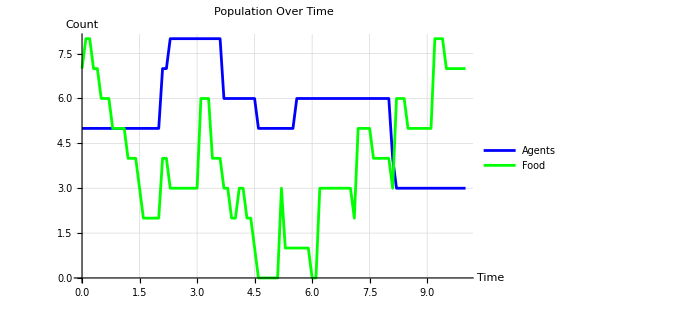

Part::partd: Part specification simulationGraphics[[101]]
     is longer than depth of object.

Part::partd: Part specification simulationGraphics[[1]]
     is longer than depth of object.

```mathematica
model = initializeModel[parameters];
Simulation = genSimulationStates[parameters, model, 100];
simulationGraphics = renderSimulation[Simulation, parameters];

Manipulate[simulationGraphics[[j]], {j, 1, Length@simulationGraphics, 1, Appearance->Labeled}]

plotPopulationStats[Simulation]
```

## Experimentation

## Conclusion

## Future Direction

## Acknowledgements

## References